Calculating and plotting NREFT form factors

```mathematica
dataF19 = Import[NotebookDirectory[] <> "FormFactors_Z=9_A=19.txt", "Table"];
dataXe129 = Import[NotebookDirectory[] <> "FormFactors_Z=54_A=129.txt", "Table"];
dataXe131 = Import[NotebookDirectory[] <> "FormFactors_Z=54_A=131.txt", "Table"];
dataXe132 = Import[NotebookDirectory[] <> "FormFactors_Z=54_A=132.txt", "Table"];

dataF19 = PadRight[dataF19, { Length[dataF19], Length[dataF19[[1]]]}];
dataXe129 = PadRight[dataXe129, { Length[dataXe129], Length[dataXe129[[1]]]}];
dataXe131 = PadRight[dataXe131, { Length[dataXe131], Length[dataXe131[[1]]]}];
dataXe132 = PadRight[dataXe132, { Length[dataXe132], Length[dataXe132[[1]]]}];

Export[NotebookDirectory[] <> "FormFactors_Z=9_A=19.dat",dataF19];
Export[NotebookDirectory[] <> "FormFactors_Z=54_A=129.dat",dataXe129];
Export[NotebookDirectory[] <> "FormFactors_Z=54_A=131.dat",dataXe131];
Export[NotebookDirectory[] <> "FormFactors_Z=54_A=132.dat",dataXe132];
```

Xe-131

0.0791728

0.

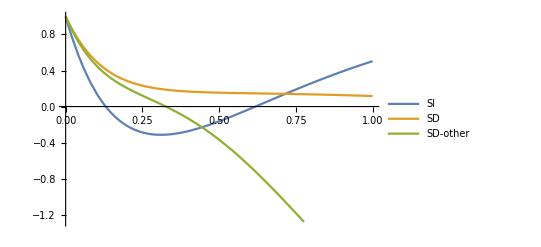

```mathematica
ClearAll[CalcFormFactor]

test[y_]:=
(
u = 2*y;
Return[(0.05 - 0.15*u + 0.23*u^2 - 0.18*u^3)*Exp[-u]];

)

CalcFormFactor[op_,target_, cp_, cn_, y_]:=
(
data = Switch[target,
"F-19", dataF19,
"Xe-129", dataXe129, 
"Xe-131", dataXe131,
"Xe-132", dataXe132];

maxpow = Length[data[[1]]] - 1;

yrange = y^Range[0,maxpow];
Fpp = data[[(op - 1)*4 + 1]];
Fpn = data[[(op - 1)*4 + 2]];
Fnp = data[[(op - 1)*4 + 3]];
Fnn = data[[(op - 1)*4 + 4]];
res = cp*cp*(yrange.Fpp);
res += cp*cn*(yrange.Fpn);
res += cn*cp*(yrange.Fnp);
res += cn*cn*(yrange.Fnn);
Return[res*Exp[-2*y]]
)

J=3/2;
t = "Xe-131"
Sp = Sqrt[(J/(4(J+1)))*(CalcFormFactor[2, t, 1, 0,1*^-10] + CalcFormFactor[3, t, 1, 0,1*^-10] )]
Sp = Sqrt[(J/(4(J+1)))*(CalcFormFactor[2, t, 0, 1,1*^-10] + CalcFormFactor[3, t, 0, 1,1*^-10] )]

Plot[{CalcFormFactor[1,t, 1, -1, y]/CalcFormFactor[1,t, 1, -1, 1*^-10],CalcFormFactor[2,t, 1, 1, y]/CalcFormFactor[2,t, 1, 1, 1*^-10], test[y]/test[0]}, {y, 0, 1}, PlotLegends->{"SI", "SD", "SD-other"}]
```

```mathematica
Xe129S00u = {0.054731, −0.146897, 0.182479, −0.128112, 0.0539978, −0.0133335, 0.00190579, −1.48373*^-4};
Xe129S00y = 2^Range[0,7]*Xe129S00u*16*1.571;

Xe129S11u = {0.02933, −0.0905396, 0.122783, −0.0912046, 0.0401076, −0.010598, 0.00168737, −1.56768*^-4};
Xe129S11y = 2^Range[0,7]*Xe129S11u*16*1.571;

Xe129S01u = {−0.0796645, 0.231997, −0.304198, 0.222024, −0.096693, 0.0251835, −0.00392356, 3.53343*^-4};
Xe129S01y = 2^Range[0,7]*Xe129S01u*16*1.571;

Xe131S00u = {0.0417889, −0.111171, 0.171966, −0.133219, 0.0633805, −0.0178388, 0.00282476, −2.31681*^-4};
Xe131S00y =  2^Range[0,7]*Xe131S00u*16*0.785;

Xe131S01u = {-0.0608808, 0.181473, -0.272533, 0.211776, -0.0985956, 0.027438, -0.0044424, 3.97619*^-4};
Xe131S01y = 2^Range[0,7]*Xe131S01u*16*0.785;

Xe131S11u = {0.022446, −0.0733931, 0.110509, −0.0868752, 0.0405399, −0.0113544, 0.00187572, −1.75285*^-4};
Xe131S11y = 2^Range[0,7]*Xe131S11u*16*0.785;



Xe129Fpp = Abs[Xe129S00y + Xe129S11y + Xe129S01y]
Xe129Fnn = Abs[Xe129S00y + Xe129S11y - Xe129S01y]
Xe129Fpn = (Xe129S00y - Xe129S11y );

Xe131Fpp = Abs[Xe131S00y + Xe131S11y + Xe131S01y]
Xe131Fnn = Abs[Xe131S00y + Xe131S11y - Xe131S01y]
Xe131Fpn = (Xe131S00y - Xe131S11y );

Xe129Fitz = {Xe129Fpp, Xe129Fpn, Xe129Fpn, Xe129Fnn};
Xe131Fitz = {Xe131Fpp, Xe131Fpn, Xe131Fpn, Xe131Fnn};


Export[NotebookDirectory[] <> "Xe129_F.dat",Xe129Fitz, "Table"];
Export[NotebookDirectory[] <> "Xe131_F.dat", Xe131Fitz, "Table"];
```

{0.11051,0.27346,0.106979,0.544426,1.04067,1.00705,0.531516,0.155086}

{4.1154,23.5994,61.2775,88.7483,76.7345,39.5057,12.0922,2.11861}

{0.0421275,0.0776484,0.499486,0.835813,1.07007,0.70545,0.207455,0.015027}

{1.57145,9.19485,27.8836,43.3943,40.6976,22.7612,7.34941,1.29352}

```mathematica
0.293^2/0.046^2
0.242^2/0.038^2
```

40.5714

40.5568

```mathematica
ξ = N[6/19];
δ = 0.017;

Fa = δ (2y)^2 - ξ (2y) + 1;
Expand[1.697*Fa^2]
```

1.697-2.14358 y+0.907712 y^2-0.145763 y^3+0.00784693 y^4